```mathematica
(*Import all simulations*)
(*Average all simulations*)
(*Extract mean, median & mode*)
(*Plot averages*)
```

```mathematica
(*Single Simulations*)
```

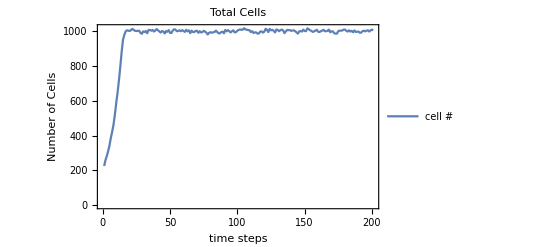

```mathematica
data=Import["/Users/arturo/Desktop/AneyploidySim0.1/CellGrowth/data normal/2 of 100.txt",{"Data",{All}}];
ListLinePlot[{data[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

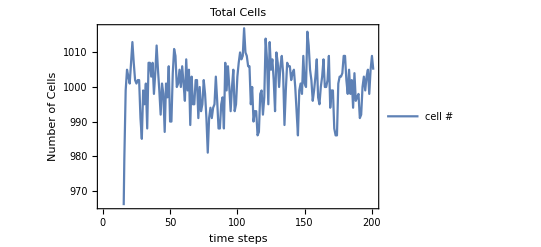

```mathematica
ListLinePlot[{data[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> Automatic, AspectRatio->1/GoldenRatio]
```

```mathematica
(*All Simualtions*)
```

```mathematica
files=FileNames["*100.txt",{"/Users/arturo/Desktop/AneyploidySim0.1/CellGrowth/data normal/"}];
dataAll=Table[Import[files[[j]],"Data"],{j,1,Length[files]}];
Length[dataAll]
```

100

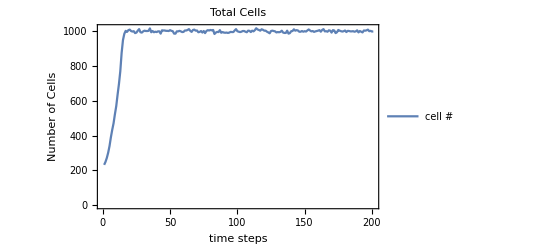

```mathematica
data2=dataAll[[2]];
ListLinePlot[{data2[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
ListLinePlot[{dataAll[[2]][[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*Average all Simulations*)
```

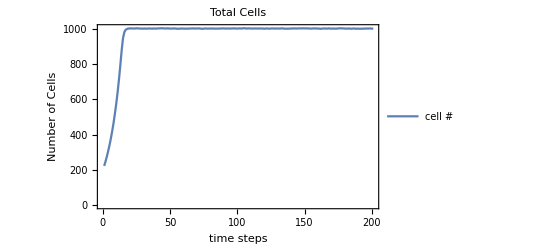

```mathematica
dataAllMean=Mean[dataAll];
ListLinePlot[{dataAllMean[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

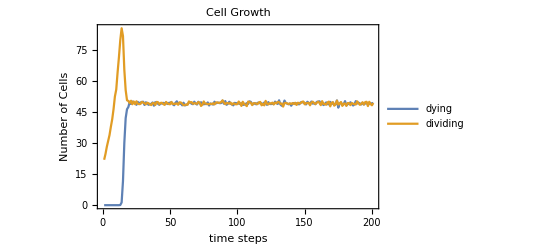

```mathematica
ListLinePlot[{dataAllMean[[All,4]],dataAllMean[[All,5]]}, PlotLegends->{"dying","dividing"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Cell Growth",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gene copy #*)
```

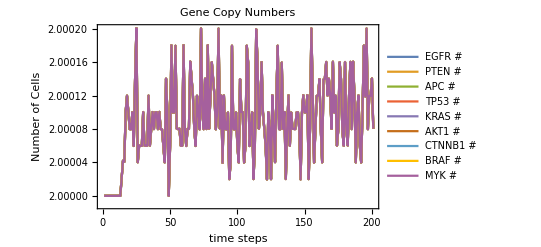

```mathematica
ListLinePlot[{
dataAllMean[[All,6]],
dataAllMean[[All,7]],
dataAllMean[[All,8]],
dataAllMean[[All,9]],
dataAllMean[[All,10]],
dataAllMean[[All,11]],
dataAllMean[[All,12]],
dataAllMean[[All,13]],
dataAllMean[[All,14]]}, PlotLegends->{"EGFR #","PTEN #","APC #","TP53 #","KRAS #","AKT1 #","CTNNB1 #","BRAF # ","MYK #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Gene Copy Numbers",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gene mutations*)
```

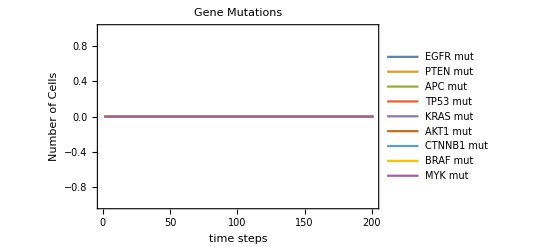

```mathematica
ListLinePlot[{
dataAllMean[[All,15]],
dataAllMean[[All,16]],
dataAllMean[[All,17]],
dataAllMean[[All,18]],
dataAllMean[[All,19]],
dataAllMean[[All,20]],
dataAllMean[[All,21]],
dataAllMean[[All,22]],
dataAllMean[[All,23]]}, PlotLegends->{"EGFR mut","PTEN mut","APC mut","TP53 mut","KRAS mut","AKT1 mut","CTNNB1 mut","BRAF mut ","MYK mut"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Gene Mutations",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
std=StandardDeviation[dataAll];
Max[std[[All,24]]]
```

46.2139

```mathematica
std[[100,24]]
```

7.17241

```mathematica
ListLinePlot[{dataAll[[2]]}]
```

-Graphics-

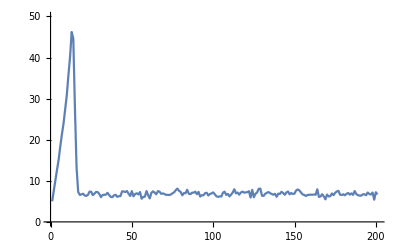

StandadDeviation[{{{200.,0.,0.,0.,28.,2.,2.,2.,2.,2.,2.,2.,2.,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,228.,},199,{907.,0.,0.,51.,47.,2.,2.,2.,2.,2.,2.,2.,2.,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1005.,}},{1},{1},94,{1},{1},{1}}]
 |  |  |  |

```mathematica
ListLinePlot[std[[All,24]], PlotRange->{0,50}]
```

```mathematica
max
```

```mathematica
μ=TimeSeriesThread[Mean,data];
σ=TimeSeriesThread[StandardDeviation,data];
```

```mathematica
[[All,24]]
```